```mathematica
FullSimplify[Integrate[Integrate[Integrate[(ni E^(-r'/ri)+n0(r'/r0)^2E^(-r'/r0))*r'^2*Sin[θ],{r',0,r}],{θ, 0, Pi}], {ϕ,0,2Pi}]]
```

2 π (48 n0 r0^3-(2 ⅇ^(-r/r0) n0 (r^4+4 r^3 r0+12 r^2 r0^2+24 r r0^3+24 r0^4))/r0+4 ni ri^3-2 ⅇ^(-r/ri) ni ri (r^2+2 r ri+2 ri^2))

```mathematica
n0=1
ni=n0*1000

ri=1
r0=1000*ri
L = 1
r = Sqrt[L/(4 Pi s)]
Nn = FullSimplify[Integrate[Integrate[Integrate[(ni E^(-r'/ri)+n0(r'/r0)^2E^(-r'/r0))*r'^2*Sin[θ],{r',0,r}],{θ, 0, Pi}], {ϕ,0,2Pi}]]
```

1

1000

1

1000

1

(√(1/s))/(2 √π)

96000008000 π-(1000 ⅇ^(-(√(1/s))/(2 √π)) (1+(4 √π)/(√(1/s))+8 π s))/s-(ⅇ^(-(√(1/s))/(2000 √π)) (1+8000 s (6000 π+(24000000 π^(3/2))/(√(1/s))+√π √(1/s)+48000000000 π^2 s)))/(4000 π s^2)

1000

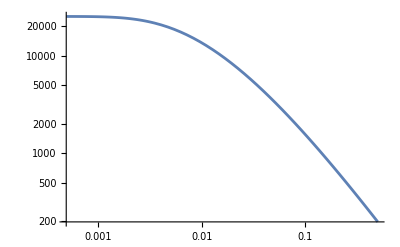

```mathematica
LogLogPlot[Nn,{s,0,0.5}]
```

```mathematica
Limit[-(2 ⅇ^(-r/r0)  (r^4+4 r^3 r0+12 r^2 r0^2+24 r r0^3+24 r0^4))/r0, r0->0]
```

ConditionalExpression[Indeterminate, r>0]

ConditionalExpression[Indeterminate, n0∈ℝ&&r>0]

ConditionalExpression[Indeterminate, n0∈ℝ&&r>0]

ConditionalExpression[Indeterminate, n0>0&&r>0]

ConditionalExpression[Indeterminate, (ni ri^3|ⅇ^(-r/ri) ni ri (r^2+2 r ri+2 ri^2))∈ℝ&&n0>0&&r>0]